# 知識構造化法課題フォロー

## フォーマットについて

レポートのフォーマットとして、記入必要事項が決めてありましたが、これを満たしていないレポートが散見されました。

## フィットについて

フィッティングとは、独立変数を使い従属変数を予測する式を、モデルとパラメータを利用して決定することです。

モデルは人間が決めなくてはなりませんが、モデルが決まるとそれに応じてパラメータを決定する方法が決まります。

もっとも簡単なモデルのひとつは、
y = a + b x
のような１次式で、xが独立変数、a、bがパラメータです。

以下は、G8のGDPを取得したものですが、ここから考えられるモデルのひとつは、8カ国のランクから実際のGDPを求めるものです。この場合、ランクを横軸とするには値がソートされていないと意味がありません。しかしながら、このソート作業を行わずにfitを実行しているレポートが見受けられました。

```mathematica
gdp=CountryData["G8","GDP"]
```

{1.5022×10^12,2.85653×10^12,3.64947×10^12,2.30306×10^12,4.91069×10^12,1.67659×10^12,2.66627×10^12,1.40967×10^13}

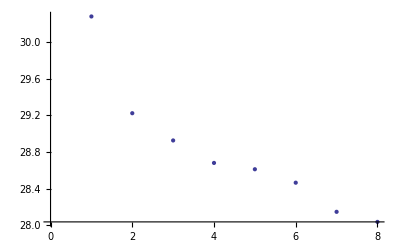

```mathematica
ListPlot[Sort[Log[gdp],Greater]]
```

```mathematica
FindFit[Sort[Log[gdp],Greater],b+a x,{a,b},x]
```

{a→-0.267813,b→30.0012}

以下はよくない例。

```mathematica
FindFit[gdp,b+a x,{a,b},x]
```

{a→9.98801×10^11,b→-2.86916×10^11}

その他、パラメータ決定の失敗を見逃しているレポートもありました。パラメータ決定には数値計算に基づく特定のアルゴリズムが用いられるので、このアルゴリズムが必ずしも行おうとしていることにマッチしているとは限りません。可視化するなどして、必ず結果を確かめましょう。上記を可視化して確かめると、そもそも、あまり良いモデルではなかったことが解ります。

## 距離行列について

距離行列を求めた結果が、行列(ランク2のテンソル)になっていない(つまり、完全な間違い)レポートがありました。

本来欲しい結果がイメージできていないために、データのチェックができなかったと思われます。手順だけを憶えるとこのような失敗を起こしがちです。距離行列は難しい概念ではないので、ちゃんと理解しておきましょう。